(* useful Global variables *)
figNo=1;
captionStyle={FontFamily→ "Book Antiqua", FontSize→16};
$Line=0;

Please note that this Notebook employs a non-default Stylesheet. Input cells with code for user-defined functions (and “useful Global variables”) are specified via ⌘-shift-D rather than ⌘-9 as for standard Input cells. They are Evaluatable Initialization cells with font size 12 and a light grey background specified by RGBColor[{0.925,0.925,0.958}].

# DB’s Noisy Gaussian Data--Digitising & Modeling

## Packages

```mathematica
Needs["IP`"]
functionListing["IP`"]
functionCount["IP`"]
```

## Functions

#### trueCoords[{x_, y_}]

ClearAll[trueCoords]
trueCoords::usage = "trueCoords[{x,y}] gives the ''true'' coordinates of the point with ''graphics'' coordinates {x,y} once the Global variables xWest, ySouth, coordsOrigin, xScaleFactor, and yScaleFactor are defined.";
trueCoords[{x_, y_}] := {(x - coordsOrigin[[1]])*xScaleFactor, (y - coordsOrigin[[2]])*yScaleFactor} + {xWest, ySouth}
trueCoords[ x_] := (x - coordsOrigin[[1]])*xScaleFactor + xWest
?trueCoords

#### egyptianFraction[ sr_ ]

egyptianFraction[] is an IP Package function.

```mathematica
?egyptianFraction
```

```mathematica
egyptianFraction[0.0043]
```

We suggest that the usefulness of expressing small errors as Egyptian fractions is simply that only the size of the denominator has to be appreciated; in the indication of the result given by Rationalize[], where the numerator is not equal to 1 some sort of division of the denominator by the numerator has to be mentally calculated in order to assess the size of the quantity, For example, …

```mathematica
{0.01615926368553744, Rationalize[0.01615926368553744, 0.00001], egyptianFraction[ 0.01615926368553744 ]}
{0.02267034975866533, Rationalize[0.02267034975866533, 0.00001], egyptianFraction[ 0.02267034975866533 ]}
{0.013655339728615434, Rationalize[0.013655339728615434, 0.00001], egyptianFraction[ 0.013655339728615434 ]}
```

#### egyptianFractionSimple[sr_]

egyptianFractionSimple[] is an IP Package function,

```mathematica
egyptianFractionSimple[0.0043]
```

We suggest that the usefulness of expressing small errors as Egyptian fractions is simply that only the size of the denominator has to be appreciated; in the indication of the result given by Rationalize[], where the numerator is not equal to 1 some sort of division of the denominator by the numerator has to be mentally calculated in order to assess the size of the quantity, For example, …

```mathematica
{0.01615926368553744, Rationalize[0.01615926368553744, 0.00001], egyptianFractionSimple[ 0.01615926368553744 ]}
{0.02267034975866533, Rationalize[0.02267034975866533, 0.00001], egyptianFractionSimple[ 0.02267034975866533 ]}
{0.013655339728615434, Rationalize[0.013655339728615434, 0.00001], egyptianFractionSimple[ 0.013655339728615434 ]}
```

#### integratedCurvature[ annFittedFunction_, {xMin_,xMax_} ]

Remove[ integratedCurvature ]
integratedCurvature::usage="integratedCurvature[arg, {xMin,xMax}] is an overloaded function.
If the first input has Head NetChain, integratedCurvature[] fits an InterpolationFunction object to a table of sampled coordinates from the ANN-derived fitted function curvetrained[x] in order to construct a curvature function κ[x] for the given function.
A simple step then creates a parametric form of the InterpolationFunction representation of the fitted function, from which the curvature function is directly derived.
If the first input has Head Symbol, integratedCurvature[] directly creates the required parametric form of the target function and then the curvature function κ[x].
Numerically integrating κ[x] over the specified domain {xMin,xMax} yields a measure of the overall ''straightness'' of the fitted function.
If two candidate fitted functions have essentially equal maximum errors across the data points, the ''straighter'' (smaller integrated absolute curvature |κ[x]|) fitted function is preferred.";
integratedCurvature[ annFittedFunction_NetChain, {xMin_,xMax_} ] := Module[ 
{interpF, x, y,κ} ,
(* construct InterpolationObject representation of annFittedFunction[x] *)
interpF = Interpolation[Table[ {x,annFittedFunction[x] }, {x,xMin,xMax,0.05} ]];
(* construct parametric form of y=interpF[x] *)
x[t_]:=t;
y[t_]:=interpF[t];
(* construct curvature function κ[x] for interpF[x] *)
κ[w_]:= (∂_t x[t] ∂_{t,2} y[t] - ∂_t y[t] ∂_{t,2} x[t])/(((∂_t x[t])^2+(∂_t y[t])^2)^(3/2))/.{t->w}//Evaluate;
(* numerically integrate absolute curvature over given domain *)
NIntegrate[ Abs[ κ[x] ], {x, xMin,xMax} ]
]

integratedCurvature[ func_Symbol, {xMin_,xMax_} ] := Module[ 
{x, y,κ},
(* construct parametric form of y=func[x] *)
x[t_]:=t;
y[t_]:=func[t];
(* construct curvature function κ[x] for func[x] *)
κ[w_]:= (∂_t x[t] ∂_{t,2} y[t] - ∂_t y[t] ∂_{t,2} x[t])/(((∂_t x[t])^2+(∂_t y[t])^2)^(3/2))/.{t->w}//Evaluate;
(* numerically integrate absolute curvature over given domain *)
NIntegrate[ Abs[ κ[x] ], {x, xMin,xMax} ]//Quiet
]
integratedCurvature[ func_InterpolatingFunction, {xMin_,xMax_} ] := Module[ 
{x, y,κ},
(* construct parametric form of y=func[x] *)
x[t_]:=t;
y[t_]:=func[t];
(* construct curvature function κ[x] for func[x] *)
κ[w_]:= (∂_t x[t] ∂_{t,2} y[t] - ∂_t y[t] ∂_{t,2} x[t])/(((∂_t x[t])^2+(∂_t y[t])^2)^(3/2))/.{t->w}//Evaluate;
(* numerically integrate absolute curvature over given domain *)
NIntegrate[ Abs[ κ[x] ], {x, xMin,xMax} ]//Quiet
]
?integratedCurvature

```mathematica
integratedCurvature[ Sinc, {-10,+10} ]
```

```mathematica
func[x_]:=Sin[x];
integratedCurvature[ func, {-10,+10} ]
```

```mathematica
func[x_]:=Sin[x] ⅇ^(-x/5);
integratedCurvature[ func, {-10,+10} ]
```

#### curvatureFunction[ func_InterpolatingFunction ]

```mathematica
Remove[ curvatureFunction ]
curvatureFunction::usage="curvatureFunction[arg] is an overloaded function.
If the input has Head NetChain (e.g., curvetrained), integratedCurvature[curvetrained] constructs the curvature function κ for the ANN fitted function curvetrained[x].
If the input has Head Symbol (e.g., func), curvatureFunction[func] constructs the curvature function κ for the function y=func[x].
If the input has Head InterpolatingFunction, (e.g., interpF) curvatureFunction[interpF] constructs the curvature function for the function y=interpF[x].
Typical usage is: kurv=curvatureFunction[ … ], followed by Plot[ kurv[x], {x, xMin, xMax}].
Note that for a general unassigned input with Head Symbol, (e.g., f) the form of the curvature function is
κ[x] = f''[x]/((1+f'[x]^2)^(3/2)),
so that the curvature is—unsurprisingly—essentially a scaled version of the second derivative.
When f'[x] = 0 (at maxima and minima) the curvature is exactly f''[x].
"; 
curvatureFunction[ func_InterpolatingFunction ] := Module[ 
{x, y,κ},
(* construct parametric form of y=func[x] *)
x[t_]:=t;
y[t_]:=func[t];
(* construct curvature function κ[x] for func[x] *)
(s↦ (D[x[t], t] D[y[t], {t,2}] - D[y[t], t] D[x[t], {t,2}])/(((D[x[t], t])^2+(D[y[t], t])^2)^(3/2))/.{t->s}//Evaluate)
]
curvatureFunction[ func_Symbol ] := Module[ 
{x, y,κ},
(* construct parametric form of y=func[x] *)
x[t_]:=t;
y[t_]:=func[t];
(* construct curvature function κ[x] for func[x] *)
(s↦ (D[x[t], t] D[y[t], {t,2}] - D[y[t], t] D[x[t], {t,2}])/(((D[x[t], t])^2+(D[y[t], t])^2)^(3/2))/.{t->s}//Evaluate)
]
curvatureFunction[ annFittedFunction_NetChain ] := Module[ 
{interpF, x, y,κ} ,
(* construct InterpolationObject representation of annFittedFunction[x] *)
interpF = Interpolation[Table[ {x,annFittedFunction[x] }, {x,xMin,xMax,0.05} ]];
(* construct parametric form of y=interpF[x] *)
x[t_]:=t;
y[t_]:=interpF[t];
(* construct curvature function κ[x] for interpF[x] *)(s↦ (D[x[t], t] D[y[t], {t,2}] - D[y[t], t] D[x[t], {t,2}])/(((D[x[t], t])^2+(D[y[t], t])^2)^(3/2))/.{t->s}//Evaluate)
]
?curvatureFunction
```

## Introduction

The creation of this Notebook was largely motivated by the desire to construct a slightly more visually appealing (in BJS’s opinion) version of graphic created by RB in the 10th version of the Volume IV PDF.

Generating this new version of the graphic for the noisy Gaussian data—which DB uses as the testbed for curve fitting using an ANN—required access to this data. An accurate reconstruction of DB’s original data was achieved by digitising it from his original graphic.

This then lead on to some experiments using SeedRandom[] and/or NetChain[]’s RandomSeeding option in order to investigate the variety of fits to this  noisy data that a particular ANN structure could produce.

W e claim that the acceptability of a given fitted function found by the ANN can be rated on the basis of:
(i) the maximum error of the fitted function at any of the data points (smaller is better), and
(ii) the integrated curvature function over the specified domain (smaller is better, on the grounds that “straighter” is better).

Section 1 below presents the digitising process which yields a list {x,y} coordinates derived directly from a suitable graphic showing DB’s noisy data.
Section 2 develops and test a curvature function for both fitted functions produce by an ANN (curvetrained[x]) and specified conventionally, as y=f[x].
Section 3 tests the curvature function applied to functions of the form y=f[x].
Section 4 tests the curvature function applied to fitted functions produced by the ANN.
Section 5 investigates fitting the DB data with an InterpolationFunction-based model.
Section 6  investigates fitting the DB data with an high order polynomial model.

These investigations required the development of two new IP package functions, integratedCurvature[] and curvatureFunction[].

## Section 1: Digitising the David Blower Noisy Gaussian Data

This is the original graphic from the draft version of Volume IV. Precise digitising of the data points (i.e., capturing their “graphics” coordinates) is facilitated by working with an enlarged version of the original graphic.
In this particular case, where the x coordinate values are known, we can obtain a quantitative measure of the precision of the digitising by comparing “true” x coordinates with their known values.

$Line = $Line-1;framedNoLabelWithCaption[ , Style[ StringForm[captionNeatFigured[ "Screenshot from draft version ofVolume IV.", 120  ],figNo++], captionStyle ],450 ]

### Setup

```mathematica
(* X "graphics" coordinate of a known point at the left end of the X axis *)
xWestCoordinate = {{24.512771867279312,451.6130874720735}}⟦1,1⟧
```

```mathematica
(* … and the xWest coordinate represents … *)
xWest = -4.0
```

```mathematica
(* X "graphics" coordinate of a known point at the right end of the X axis *)
xEastCoordinate = {{1467.0236397332953,454.4346630824597}}⟦1,1⟧
```

```mathematica
(* … and the xEast coordinate represents … *)
xEast = +4.0
```

```mathematica
(* Y "graphics" coordinate of a known point at the lower end of the Y axis... *)
ySouthCoordinate = {{751.6953557984441,11.891761540687185}}⟦1,2⟧
```

```mathematica
(* … and the ySouth coordinate represents … *)
ySouth = -1.0
```

```mathematica
(* Y "graphics" coordinate of a known point at the upperop end of the Y axis... *)
yNorthCoordinate = {{761.3130074960213,894.2852279141418}}⟦1,2⟧
```

```mathematica
(* … and the yNorth coordinate represents … *)
yNorth = 1.0
```

```mathematica
(* Set up the coordinates of the three known points, using generic variable names... *)
coordsOrigin = {xWestCoordinate, ySouthCoordinate}
coordsEast = {xEastCoordinate, ySouthCoordinate}
coordsNorth = {xWestCoordinate, yNorthCoordinate}
```

These three points should have roughly the following spatial disposition:

$Line = $Line-1;codeInTextCell[  "These three points should have roughly the spatial disposition shown in Figure",figNo,"." ]

$Line = $Line-1;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "The dispositions of coordsNorth,
coordsOrigin and coordsEast.", 120  ],figNo++], captionStyle ],300 ]

We now find the scale factors which convert differences in "graphics" coordinates along either axis into differences in "real" coordinates...

```mathematica
xScaleFactor = (xEast - xWest)/(coordsEast⟦1⟧ - coordsOrigin⟦1⟧)
```

```mathematica
yScaleFactor = (yNorth - ySouth)/(coordsNorth⟦2⟧ - coordsOrigin⟦2⟧)
```

### Checking

trueCoords[] converts digitised coordinates to “true” coordinates with respect to the axes and scaling in the original graphic plot.

```mathematica
?trueCoords
```

```mathematica
trueCoords[ coordsOrigin ]
```

```mathematica
trueCoords[ coordsEast ]
```

```mathematica
trueCoords[ coordsNorth ]
```

### Data Digitisation & Conversion

These are the “graphics” coordinates of the 10 data points:

```mathematica
graphicRawCoords = {{28.877953858117422,455.2906854960993},{97.30584125573138,422.03747602066085},{171.09468356836214,381.74741730866606},{243.69231112662197,451.3722132495325},{315.5437828129173,367.1083828744046},{386.6277048051187,356.0565701998197},{459.51901732007315,439.34369678986366},{532.3053148057725,611.0853160629924},{602.771511240902,626.0004824124849},{674.5891907955506,818.77820900159},{747.6655682946881,925.816302090289},{821.1909802211314,918.7110094684482},{892.8033464654557,706.2742470417948},{964.8324711030705,590.3925711694266},{1036.732626368857,501.9200537700597},{1110.4837010049412,505.67835872465383},{1181.4537809105682,597.988051846496},{1255.0456989864335,575.069608248197},{1325.9054069845083,395.2568579345008},{1398.39522315566,219.61020914713527},{1470.5322265624998,503.3807633011429}}
```

These are the “real” coordinates of the 10 data points:

```mathematica
graphicdataConverted = Sort[ Map[ trueCoords,  graphicRawCoords ] ]
Dimensions[graphicdataConverted]
```

An indication of the sizes of the digitising errors can be obtained if we take into account that it is known that the abscissa of the 21 data points are regularly spaced between -4 and +4 with a regular spacing of 0.4. The converted graphical data can be corrected by simply rounding the absence of values to tolerance of 0.1.

```mathematica
noisyGaussianDataDB = Map[ (s↦{Round[  s⟦1⟧, 0.1], s⟦2⟧}), graphicdataConverted]
```

We can express the differences between the digitised and true abscissæ in two ways, by (i) Rationalize[]-ing the differences with a small tolerance (here 0.00001), or (ii) expressing the differences as Egyptian fractions; the differences between these two expressions is very small.

```mathematica
Map[  First, graphicdataConverted - noisyGaussianDataDB ]
Map[  First, graphicdataConverted - noisyGaussianDataDB ]//(s↦Rationalize[s, 0.00001])
Map[  First, graphicdataConverted - noisyGaussianDataDB ] //egyptianFraction
(Map[  First, graphicdataConverted - noisyGaussianDataDB ]//(s↦Rationalize[s, 0.00001]))-
(Map[  First, graphicdataConverted - noisyGaussianDataDB ] //egyptianFraction)
```

We suggest that the usefulness of expressing small errors as Egyptian fractions is simply that only the size of the denominator has to be appreciated; in the indication of the result given by Rationalize[], where the numerator is not equal to 1 some sort of division of the denominator by the numerator has to be mentally calculated in order to assess the size of the quantity, For example, …

```mathematica
{0.01615926368553744, Rationalize[0.01615926368553744, 0.00001], egyptianFractionSimple[ 0.01615926368553744 ]}
{0.02267034975866533, Rationalize[0.02267034975866533, 0.00001], egyptianFractionSimple[ 0.02267034975866533 ]}
{0.013655339728615434, Rationalize[0.013655339728615434, 0.00001], egyptianFractionSimple[ 0.013655339728615434 ]}
```

The mean digitising error in the abscissæ, as both a Real and an Egyptian fraction,  is …

```mathematica
{Mean[Map[  (s↦ Abs[  First[ s ]]), graphicdataConverted - noisyGaussianDataDB ]],
Mean[Map[  (s↦ Abs[  First[ s ]]), graphicdataConverted - noisyGaussianDataDB ]]//egyptianFractionSimple}
```

$Line = $Line-1;codeInTextCell[ "Figure",figNo,"shows the digitised noisy Gaussian data points in DB's Figure (the gridlines indicating the abscissa values that range from -4 to +4 in steps of  0.4) along with the Gaussian function." ]

$Line = $Line-1;
Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ , GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ ⅇ^(-x^2), {x, -4,4}, PlotStyle→{Thickness[0.005],Dotted,Blue},Axes->True ]
},
PlotRange→{{-4,4}, {-1,1}},Axes->True, ImageSize->450, Frame→True,FrameLabel->{"x","y"}, AspectRatio->0.70 ];
Labeled[ %, Style[ StringForm["Figure `1`. The digitised data",figNo++], captionStyle] ]//Print

Compare with …

$Line = $Line-1;framedNoLabelWithCaption[ , Style[ StringForm[captionNeatFigured[ "Screenshot from draft version ofVolume IV.", 120  ],figNo++], captionStyle ],450 ]

$Line = $Line-1;codeInTextCell[ "Figure",figNo,"is a screenshot from the published version of Volume IV, showing our rendition of DB's original." ]

$Line = $Line-1;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "A screenshot of Figure 54.2 as it appears in the published version of Volume IV.", 60  ],figNo++], captionStyle ],450 ]

BJS Is of the opinion that the solid lines of the grid in this graphic are somewhat intrusive, and suggest that something like the proceeding figure for is a little nicer on the eye!!!

## Section 2: Curvature Functions: Development & Testing

### Arc Length

$Line = $Line-1;
codeInTextCell999[
{
{ "Figures",figNo},{"and",figNo+1},{"are screenshots from",URL["https://calcworkshop.com/vector-functions/arc-length-parameterization/"]},{"showing the theory behind our calculations of arc lenth."}
}
]

$Line = $Line-1;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from
`2`.", 120  ],figNo++, URL["https://calcworkshop.com/vector-functions/arc-length-parameterization/"]], captionStyle ],550 ]

$Line = $Line-1;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from
`2`.", 120  ],figNo++, URL["https://calcworkshop.com/vector-functions/arc-length-parameterization/"]], captionStyle ],550 ]

This simple step creates a parametric representation of a target function y = f[x], in this example, y = Sin[x].

```mathematica
Remove[x,y]
x[t_]:=t
y[t_]:=Sin[t]
```

Check the first derivatives …

```mathematica
{D[x[t], t], D[y[t], t]}
```

… and their squares;

```mathematica
{(D[x[t], t])^2,(D[y[t], t])^2}
```

A plot is always useful:

$Line = $Line-1;
Plot[ y[t], {t, 0, 2π}, Frame->True ];
Labeled[ %, Style[ StringForm["Figure `1`. Sin[x], 0 ≤ x ≤ 2π.",figNo++], captionStyle] ]//Print

The argument of the arc length integral is …

```mathematica
√((D[x[t], t])^2+(D[y[t], t])^2)
```

The arc length of one cycle of Sin[t] is …

```mathematica
∫_0^(2π) √((D[x[t], t])^2+(D[y[t], t])^2)ⅆt
%//N
```

We can define a more general arc length function for y = Sin[x].

```mathematica
Remove[ arcLength ]
arcLength[tt_]:= ∫_0^tt √((D[x[t], t])^2+(D[y[t], t])^2)ⅆt//Evaluate
```

This checks that different arc lengths are sensible.

```mathematica
arcLength[π/2]
%//N
```

```mathematica
arcLength[π]
%//N
```

```mathematica
arcLength[2π]
%//N
```

### Developing an Integrated Curvature Function Based on y=func[x]

https://en.wikipedia.org/wiki/Curvature

$Line = $Line-1;codeInTextCell[ "Figure",figNo,"shows a Wikipedia screenshot giving the theory behind our calculation of the curvature function κ[x]." ]

$Line = $Line-1;framedNoLabelWithCaption[ -Graphics-, Style[ StringForm[captionNeatFigured[ "Screenshot from `2`.", 120  ],figNo++, URL["https://en.wikipedia.org/wiki/Curvature"]], captionStyle ],550 ]

Based on x[t] and y[t] as specified above, the (signed) curvature formula gives …

```mathematica
(D[x[t], t] D[y[t], {t,2}] - D[y[t], t] D[x[t], {t,2}])/(((D[x[t], t])^2+(D[y[t], t])^2)^(3/2))
```

```mathematica
∫_0^(2π) Abs[ -Sin[t]/((1+Cos[t]^2)^(3/2)) ]ⅆt
%//N
```

The code for the IP package function integratedCurvature[] clearly shows the steps involved in:
(i) creating a parametric representation of the target function func, of the form {x[t], y[t}, as above;
(ii) constructing the corresponding (signed) curvature function κ[w]; and
(iii) numerically integrating |κ[w]|over the specified domain.

integratedCurvature[ func_Symbol, {xMin_,xMax_} ] := Module[ 
{x, y,κ},
(* construct parametric form of y=func[x] *)
x[t_]:=t;
y[t_]:=func[t];
(* construct curvature function κ[x] for func[x] *)
κ[w_]:= (∂_t x[t] ∂_{t,2} y[t] - ∂_t y[t] ∂_{t,2} x[t])/(((∂_t x[t])^2+(∂_t y[t])^2)^(3/2))/.{t->w}//Evaluate;
(* numerically integrate absolute curvature over given domain *)
NIntegrate[ Abs[ κ[x] ], {x, xMin,xMax} ]//Quiet
]

Testing integratedCurvature[func,{0,2π}]:

```mathematica
func[x_]:=Sin[x];
integratedCurvature[ func, {0,2π} ]
```

An Aside

Mathematica has the system function ArcCurvature[].

```mathematica
ArcCurvature[ func[t],t]
```

```mathematica
curvatureFunction[ func ][t]
```

```mathematica
NIntegrate[ ArcCurvature[ func[t],t], {t, 0, 2π} ]
```

```mathematica
NIntegrate[ ArcCurvature[ func[t],t], {t, 0, 2π} ] - integratedCurvature[ func, {0,2π} ]
Precision[%]
```

```mathematica
Plot[ {func[t]//Evaluate,ArcCurvature[ func[t],t]//Evaluate},{t, 0, 2π} , Frame->True]
```

```mathematica
Plot[ {func[t],curvatureFunction[ func ][t]//Evaluate},{t, 0, 2π},Frame->True ]
```

```mathematica
Plot[ ( Abs[ curvatureFunction[ func ][t] ]-ArcCurvature[ func[t],t])//Evaluate,{t, 0, 2π},Frame->True ]
```

```mathematica
Abs[ curvatureFunction[ func ][t] ]-ArcCurvature[ func[t],t]
```

Mathematica doesn’t recognise that Abs[] and RealAbs[] are essentially the same functions when the arguments are real:

```mathematica
Abs[ curvatureFunction[ func ][t] ]-ArcCurvature[ func[t],t]//FunctionExpand//Simplify
```

However, with reals arguments, their series expansions tell the story:

```mathematica
Assuming[  t∈Reals, Series[  Abs[Sin[t]]/(Abs[1+Cos[t]^2]^(3/2))//FunctionExpand, {t, 0, 13}]//Normal ]⟦1,1,1⟧
```

```mathematica
Assuming[  t∈Reals, Series[  RealAbs[Sin[t]]/((1+Cos[t]^2)^(3/2))//FunctionExpand, {t, 0, 13}]//Normal ]⟦1,1,1⟧
```

```mathematica
%%-%
```

### Developing an Integrated Curvature Function Based on curvetrained[x]

Note t	hat for the numerical coordinate data in noisyGaussianDataDB to be available to NetTrain[] in the correct form the coordinate data points {x, y} must each be expressed in terms of Rule[]s of the form x → y.

```mathematica
noisyGaussianDataDBAsRules = Map[ (s↦s⟦1⟧->s⟦2⟧), noisyGaussianDataDB ]
```

We need an example of a fitted function found by the ANN.
This finds an ANN fitted function—curvetrained[x]—based on RandomSeeding→16.
The essential code is …

curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding->23983
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding->23983
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];
autoCollapse[];
Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print
(**)
differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB]
Map[ egyptianFractionSimple, differences]
MinMax[Abs[ Map[ egyptianFractionSimple, differences]]]

curvetrained[x] is the fitted function found by the ANN:

$Line=$Line-3;
Plot[ curvetrained[x], {x, -4,+4} , Frame->True];
Labeled[ %, Style[ StringForm["Figure `1`. curvetrained[x] in the interval -4 ≤ x ≤+4.",figNo++], captionStyle] ]//Print

interpF[] is an interpolation function fitted to these points …

$Line=$Line-3;
ListPlot[ Table[ {x, curvetrained[x]}, {x,-4,4,0.05}], Frame->True ];
Labeled[ %, Style[ StringForm["Figure `1`. curvetrained[x] regularly sampled 161
times in the interval -4 ≤ x ≤+4.",figNo++], captionStyle] ]//Print

… regularly sampled from curvetrained[x].

We need an InterpolatingFunction representation of curvetrained[x] because we will need to be able to calculate first and second derivatives of the underlying function in order to obtain the curvature function κ[s].

Although curvetrained[x] looks like a function of x it has in fact a very large and complex structure …

```mathematica
curvetrained//Length
curvetrained//ByteCount
```

… and cannot be symbolically differentiated:

```mathematica
D[curvetrained[x], x]
```

By contrast, Mathematica’s InterpolatingFunction objects can be differentiated.

We first need a list of {x,y} regularly sampled points along the fitted function:

```mathematica
Table[ {x,curvetrained[x] }, {x,-4,4,0.05} ]//Short
```

This creates the function interpF[]:

```mathematica
Remove[ interpF ]
interpF = Interpolation[Table[ {x,curvetrained[x] }, {x,-4,4,0.05} ]]
```

$Line = $Line-1;codeInTextCell[ "Figure",figNo,"shows curvetrained[x] and interpF[x], with the latter slightly displaced downwards for clarity. interpF[x] appears to be an accurate representation of curvetrained[x]." ]

$Line=$Line-3;
Plot[ {curvetrained[x],interpF[x]-0.1},{x,-4,4}, Frame->True, PlotLegends->"Expressions"];
Labeled[ %, Style[ StringForm["Figure `1`. curvetrained[x] and interpF[x] (displaced)
in the interval -4 ≤ x ≤+4.",figNo++], captionStyle] ]//Print

$Line = $Line-1;codeInTextCell[ "Figure",figNo,"shows the difference curvetrained[x] - interpF[x]; the largest absolute discrepancy ~ 0.003, confirming that interpF[x] is an accurate numerical representation of curvetrained[x]." ]

$Line=$Line-3;
Plot[ curvetrained[x]-interpF[x],{x,-4,4}, Frame->True, PlotRange->All ];
Labeled[ %, Style[ StringForm[ "Figure `1`. curvetrained[x] - interpf[x]
in ther interval -4 ≤ x ≤ +4.",figNo++], captionStyle] ]//Print

This simple step gives us a parametric representation of curvetrained[x] (in the guise of interpF[]) in terms of x[t] and y[t]:

```mathematica
Remove[x,y]
x[t_]:=t
y[t_]:=interpF[t]
```

Since curvetrained[x] cannot be differentiated, the following code does not work. This is why we need a high fidelity differentiable InterpolationFunction[] representation of curvetrained.

Remove[x, y]
x[t_] := t
y[t_] := curvetrained[t] and

{∂_u x[u], ∂_u y[u]}
NetChain::invindata3: "Data supplied to port "Input" could not be encoded; input was not a list of numeric values."
{1,0}
{∂_{u,2} x[u], ∂_{u,2} y[u]}
NetChain::invindata3: "Data supplied to port "Input" could not be encoded; input was not a list of numeric values."
{0,0}

Checking …

```mathematica
{x[t],y[t]}
```

To construct a curvature function κ[t] we need first and second derivatives of x[t] and y[t].

```mathematica
{D[x[u], u], D[y[u], u]}
```

```mathematica
{D[x[u], {u,2}], D[y[u], {u,2}]}
```

$Line = $Line-1;codeInTextCell[ "Figure",figNo,"shows curvetrained[x] and the first derivative of curvetrained[x]." ]

$Line=$Line-3;
Plot[ {4 curvetrained[x],∂_u y[u]/.{u->x}},{x,-4,4}, ImageSize->400, Frame->True, PlotRange->{{-4,+4},All}, PlotLegends->"Expressions"];
Labeled[ %, Style[ StringForm[ "Figure `1`. curvetrained[x] (scaled) and its first derivative
wrt x in ther interval -4 ≤ x ≤ +4.",figNo++], captionStyle] ]//Print

$Line = $Line-1;codeInTextCell[ "Figure",figNo,"shows curvetrained[x] (scaled for clarity) and the second derivative of curvetrained[x]." ]

$Line=$Line-3;Plot[ {50 curvetrained[x], ∂_{u,2} y[u]/.{u->x}},{x,-4,4},ImageSize->400, Frame->True,PlotRange->All, PlotLegends->"Expressions"];
Labeled[ %, Style[ StringForm[ "Figure `1`. curvetrained[x] (scaled) and its second derivative
wrt x in ther interval -4 ≤ x ≤ +4.",figNo++], captionStyle] ]//Print

With the first and second derivatives of x[t] and y[t] now available, this defines the curvature function κ[x]:

```mathematica
Remove[κ]
κ[x_]:= (D[x[t], t] D[y[t], {t,2}] - D[y[t], t] D[x[t], {t,2}])/(((D[x[t], t])^2+(D[y[t], t])^2)^(3/2))/.{t->x}//Evaluate
κ[x]
```

$Line = $Line-1;codeInTextCell[ "Figure",figNo,"shows curvetrained[x] (scaled for clarity) and its curvature κ[x].
In the region near x=-1.9 it is clear that curvetrained[x] is essentially straight, and so the corresponding  curvature is nearly zero. Corresponding to the peak of curvetrained[x] near x = -0.25, κ[x] dips sharply to around -47." ]

$Line=$Line-3;Plot[ {50curvetrained[t],κ[t]}, {t, -4,4}, PlotRange->All,ImageSize->400, Frame->True, PlotLegends->"Expressions" ];
Labeled[ %, Style[ StringForm[ "Figure `1`. curvetrained[x] (scaled) and its
curvature κ[x] in the interval -4 ≤ x ≤ +4.",figNo++], captionStyle] ]//Print

Our measure of “straightness” of a fitted function will be the absolute curvature function |κ[x]| integrated over the specified domain.

$Line=$Line-3;Plot[ {50curvetrained[t],Abs[κ[t]]}, {t, -4,4}, PlotRange->All, Frame->True, PlotLegends->"Expressions" ];
Labeled[ %, Style[ StringForm[ "Figure `1`. curvetrained[x] (scaled) and the absolute value
of the curvature κ[x] in the interval -4 ≤ x ≤ +4.",figNo++], captionStyle] ]//Print

These calculations leading to a curvature function κ[x] finally allow the numerical evaluation of a “goodness-of-fit” criterion for any function fitted to a set of {x,y} data points as here.

We claim that the “straightest” fitted function found by the ANN, as long as the largest error at any of the data points in acceptable, should be preferred.

Our numerical measure of “straightness” is the integrated absolute curvature |κ[x]| over the domain of interest. In the present case, this is …

```mathematica
NIntegrate[ Abs[ κ[x] ], {x, -4,+4} ]
```

Its integrated curvature according to the defined function integratedCurvature[] is also …

```mathematica
integratedCurvature[ curvetrained, {-4,+4} ]
```

Incidentally, the precise relationship between the curvature and the second derivative of a function y = f[x] at a given abscissa is revealed as follows:

```mathematica
x[t_]:=t
y[t_]:=f[t]
Remove[ κ ]
κ[w_]:= (D[x[t], t] D[y[t], {t,2}] - D[y[t], t] D[x[t], {t,2}])/(((D[x[t], t])^2+(D[y[t], t])^2)^(3/2))/.{t->w}//Evaluate
κ[x]
```

κ[x] is a scaled version of f''[x]; when f'[x]=0 it is exactly f''[x].

## Section 3: Integrated Curvature: 3 Examples for y=func[x]

As detailed above, the overloaded form of integratedCurvature[] can accept a Symbol—usually func—as its first argument. Here are three examples if its use for functions given as y = func[x].

### Example C: y = f[x] = Sin[x]

Define the target function.

```mathematica
Remove[func]
func[x_] := Sin[x]
```

Construct a parametric representation of the target function.

```mathematica
Remove[x,y]
x[t_]:=t
y[t_]:=func[t]
```

Construct the curvature function κ[x].

```mathematica
Remove[κ]
κ[x_]:= (D[x[t], t] D[y[t], {t,2}] - D[y[t], t] D[x[t], {t,2}])/(((D[x[t], t])^2+(D[y[t], t])^2)^(3/2))/.{t->x}//FullSimplify//Evaluate
κ[x]
```

$Line = $Line-1;codeInTextCell999[ {{"Figure",figNo},{"shows the ''target'' function", Style[ func[x]//Evaluate,FontSize→14]}, {"(blue) with its corresponding curvature function",Style[κ[x]//HoldForm,FontSize→14], "(orange)." }}]

$Line=$Line-4;
{xMin,xMax}={-2π, +2π};
Plot[ {func[x]//Evaluate, κ[x]//Evaluate}, {x, xMin,xMax}, PlotRange->All,ImageSize->400, Frame->True, PlotLegends->"Expressions" ];
Labeled[ %, Style[ StringForm[ "Figure `1`. `2` and its curvature `3` in the interval `4` ≤ x ≤ `5`.",figNo++, Style[ func[x], RGBColor[0.368417, 0.506779, 0.709798]],Style[ "κ[x]", RGBColor[0.880722, 0.611041, 0.142051]], xMin,xMax], captionStyle] ]//Print

$Line = $Line-1;codeInTextCell[ "The integrated curvature of the function",func[x]//Evaluate,"over the specified domain s …" ]

```mathematica
integratedCurvature[ func, {-10,10} ]
```

### Example C: y = f[x] = Sin[x] ⅇ^(-x/5)

```mathematica
Remove[func]
func[x_] := Sin[x] ⅇ^(-x/5)
```

```mathematica
Remove[x,y]
x[t_]:=t
y[t_]:=func[t]
```

```mathematica
Remove[κ]
κ[x_]:= (D[x[t], t] D[y[t], {t,2}] - D[y[t], t] D[x[t], {t,2}])/(((D[x[t], t])^2+(D[y[t], t])^2)^(3/2))/.{t->x}//FullSimplify//Evaluate
κ[x]
```

$Line = $Line-1;codeInTextCell999[ 
{
{"Figure",figNo},
{"shows the ''target'' function", Style[ func[x] //Evaluate,FontSize→14]}, {"(blue) with its corresponding curvature function",Style[κ[x]//HoldForm,FontSize→14]},
{"(orange)." }
}
]

$Line=$Line-4;
{xMin,xMax}={-2π, +2π};Plot[ {func[x]//Evaluate,  κ[x]//Evaluate}, {x, xMin,xMax}, PlotRange->All,ImageSize->400, Frame->True, PlotLegends->"Expressions" ];
Labeled[ %, Style[ StringForm[ "Figure `1`. `2` and its curvature `3` in the interval `4` ≤ x ≤ `5`.",figNo++, Style[ func[x], RGBColor[0.368417, 0.506779, 0.709798]],Style[ "κ[x]", RGBColor[0.880722, 0.611041, 0.142051]], xMin,xMax], captionStyle] ]//Print

$Line = $Line-1;codeInTextCell[ "The integrated curvature of the function",Style[ func[x] //Evaluate,FontSize→14],"over the specified domain is …" ]

```mathematica
integratedCurvature[ func, {-2π,+2π} ]
```

Note that the progressive “compression” of the sine function by the negative exponential has a “straightening” effect on the sine function, with the result that the integrated curvature from -2π  to +2π  is somewhat less than the value 8.61394 for “uncompressed” Sin[x] .

### Example C: y = f[x] = Sinc[x]

```mathematica
Remove[func]
func[x_] :=  Sinc[x]
```

```mathematica
Remove[x,y]
x[t_]:=t
y[t_]:=func[t]
```

```mathematica
Remove[κ]
κ[x_]:= (D[x[t], t] D[y[t], {t,2}] - D[y[t], t] D[x[t], {t,2}])/(((D[x[t], t])^2+(D[y[t], t])^2)^(3/2))/.{t->x}//FullSimplify//Evaluate
κ[x]
```

$Line = $Line-1;codeInTextCell999[ {{"Figure",figNo},{"shows the ''target'' function", Style[ func[x]//Evaluate,FontSize→14]}, {"(blue) with its corresponding curvature function",Style[κ[x]//HoldForm,FontSize→14], "(orange)." }}]

$Line=$Line-4;
{xMin,xMax}={-10, +10};Plot[ {func[x]//Evaluate,  κ[x]//Evaluate}, {x, xMin,xMax}, PlotRange->All,ImageSize->400, Frame->True, PlotLegends->"Expressions" ];
Labeled[ %, Style[ StringForm[ "Figure `1`. `2` and its curvature `3` in the interval `4` ≤ x ≤ `5`.",figNo++, Style[ func[x], RGBColor[0.368417, 0.506779, 0.709798]],Style[ "κ[x]", RGBColor[0.880722, 0.611041, 0.142051]], xMin,xMax], captionStyle] ]//Print

$Line = $Line-1;codeInTextCell[ "The integrated curvature of the function",Style[ func[x]//Evaluate,FontSize→14],"over the specified domain is …" ]

```mathematica
integratedCurvature[ func, {-10,10} ]
```

## Section 4: Integrated Curvature: 18 Examples for y=curvetrained[x]

In this section we repeatedly train a neural net to fit a continuous curve through the 21 data points shown above.
The WDC page for NetInitialize[] states: “NetInitialize typically assigns random values to parameters representing weights and zero to parameters representing biases. ”
In view of its use of random values we investigate the particular dependence on the random values values used to initialise the network by repeatedly running a code block in which the random number seed set by the NetChain[] option RandomSeeding is varied. The results vary accordingly.

The best fitting models found by the new network do look like good fits to the data. The first seven or eight data points proved to be more troublesome then the rest of the data set in finding an adequate fitting function.
Those networks for which the argument of seed random is a five digit random digit were found using what is obviously random search. For the other networks, the code block was included in a For[] loop with the argument of SeedRandom[] running from 1 to 40. The fits shown below were some of the worst and best.

### RandomSeeding→15 (1/10, 12.6086)

This model is typical of the poorly fitting models we found both in the loop discussed above and using random search for the seed random arguments. The poorest fit always seems to involve the first six or seven data points.

The numerical data underneath each figure consists of the following.
(i) a list of the differences between the fitted function and the data ordinate values for the 21 data points;
(ii) The difference values (i) rendered as Egyptian fractions; and 
(iii) The minimum and maximum values in the list of Egyptian fractions, shown so as to make easy a quick assessment of the quality of the fit.
We characterise the fit quality by the worst difference, again expressed as an Egyptian fraction, together with the “integrated curvature” as a measure of the overall “straightness” of the fitted function. Low values of “integrated curvature” are good; just as low values of the worst difference at a data point.

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
     LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 15
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding→15
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];

Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

### RandomSeeding→16 (1/72, 16.5828)

Model produced by this setting of seed random overall has a good fit but requires a rather large and unnecessary looking excursion between x =  0 and x =  0.4.

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
     LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 16
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding→16
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];

Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

### RandomSeeding→80167 (1/9, 12.1948)

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
     LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 80167
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding→80167
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];

Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

### RandomSeeding→42434 (1/9, 13.028)

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
     LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 42434
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding→42434
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];

Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

### RandomSeeding→37 (1/10, 12.4112)

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
     LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 37
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding→37
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];

Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

### RandomSeeding→43 (1/9, 13.5898)

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
     LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 43
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding→43
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];

Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

### RandomSeeding→159 (1/11, 12.1499)

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
     LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 159
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding→159
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];

Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

### RandomSeeding→90987 (1/51, 16.6038)

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
     LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 90987
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding→90987
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];

Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

```mathematica
90987
```

### RandomSeeding→12 (1/53, 16.1872)

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
     LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 12
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding→12
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];

Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

```mathematica
90987
```

### RandomSeeding→44332 (1/51, 15.5277)

This model is overall a good fit to the data, but seems to require what would appear to be an unnecessary minimum and maximum between x = -0.4 and x = 0.

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
     LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 44332
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding→44332
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];

Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

```mathematica
90987
```

### RandomSeeding→44329 (1/9, 12.3779)

This model is overall a good fit to the data, but seems to require what would appear to be an unnecessary minimum and maximum between x = -0.4 and x = 0.

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
     LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 44329
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding→44329
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];

Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

```mathematica
90987
```

### RandomSeeding→17 (1/25, 13.8195)

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
     LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 17
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding→17
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];

Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

```mathematica
90987
```

### RandomSeeding→24 (1/319, 14.1759)

This is the best model found in this investigation.
Note the absence of extreme excursions between the data points.

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
     LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 24
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding→24
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];

Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

```mathematica
90987
```

### RandomSeeding→432 (1/54, 17.6452)

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
     LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 432
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding→432
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];

Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

#### SeedRandom[16] + LinearLayer[200] (1/103)

With SeedRandom[16] the ANN with a structure based on LinearLayer[100] gave a very good worst-fit value of 1/78.
Allowing a larger ANN with LinearLayer[200] and SeedRandom[16] gave a better fit (1/103), although not as good as the best model found (1/353) with LinearLayer[100] and SeedRandom[24].
This model is overall a good fit, except for the large excursion between x = -0.4 and x = 0.

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[200], ElementwiseLayer[Tanh] ,
     LinearLayer[200], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 16
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[200], ElementwiseLayer[Tanh] ,
LinearLayer[200], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding->16
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];
(*autoCollapse[];*)
Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

### RandomSeeding→192938 (1/9, 13.2975)

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
     LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 192938
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding→192938
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];

Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

#### SeedRandom[16] + LinearLayer[200] (1/103)

With SeedRandom[16] the ANN with a structure based on LinearLayer[100] gave a very good worst-fit value of 1/78.
Allowing a larger ANN with LinearLayer[200] and SeedRandom[16] gave a better fit (1/103), although not as good as the best model found (1/353) with LinearLayer[100] and SeedRandom[24].
This model is overall a good fit, except for the large excursion between x = -0.4 and x = 0.

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[200], ElementwiseLayer[Tanh] ,
     LinearLayer[200], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 16
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[200], ElementwiseLayer[Tanh] ,
LinearLayer[200], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding->16
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];
(*autoCollapse[];*)
Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

```mathematica
192938
```

### RandomSeeding→86411 (1/9, 12.961)

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
     LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 86411
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding→86411
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];

Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

#### SeedRandom[16] + LinearLayer[200] (1/103)

With SeedRandom[16] the ANN with a structure based on LinearLayer[100] gave a very good worst-fit value of 1/78.
Allowing a larger ANN with LinearLayer[200] and SeedRandom[16] gave a better fit (1/103), although not as good as the best model found (1/353) with LinearLayer[100] and SeedRandom[24].
This model is overall a good fit, except for the large excursion between x = -0.4 and x = 0.

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[200], ElementwiseLayer[Tanh] ,
     LinearLayer[200], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 16
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[200], ElementwiseLayer[Tanh] ,
LinearLayer[200], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding->16
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];
(*autoCollapse[];*)
Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

```mathematica
192938
```

### RandomSeeding→56453 (1/26, 14.5094)

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
     LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 56453
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding→56453
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];

Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

#### SeedRandom[16] + LinearLayer[200] (1/103)

With SeedRandom[16] the ANN with a structure based on LinearLayer[100] gave a very good worst-fit value of 1/78.
Allowing a larger ANN with LinearLayer[200] and SeedRandom[16] gave a better fit (1/103), although not as good as the best model found (1/353) with LinearLayer[100] and SeedRandom[24].
This model is overall a good fit, except for the large excursion between x = -0.4 and x = 0.

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[200], ElementwiseLayer[Tanh] ,
     LinearLayer[200], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 16
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[200], ElementwiseLayer[Tanh] ,
LinearLayer[200], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding->16
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];
(*autoCollapse[];*)
Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

```mathematica
192938
```

### RandomSeeding→16; LinearLayer[200] (1/71, 16.5828)

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[200], ElementwiseLayer[Tanh] ,
     LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 16
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[100], ElementwiseLayer[Tanh] ,
LinearLayer[100], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding→16
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];

Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

```mathematica
2 2
```

differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

```mathematica
2 2
```

$Line=$Line-2;
inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

```mathematica
2 2
```

$Line=$Line-2;
inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

```mathematica
2 2
```

$Line=$Line-2;
inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

```mathematica
2 2
```

#### SeedRandom[16] + LinearLayer[200] (1/103)

With SeedRandom[16] the ANN with a structure based on LinearLayer[100] gave a very good worst-fit value of 1/78.
Allowing a larger ANN with LinearLayer[200] and SeedRandom[16] gave a better fit (1/103), although not as good as the best model found (1/353) with LinearLayer[100] and SeedRandom[24].
This model is overall a good fit, except for the large excursion between x = -0.4 and x = 0.

$Line = $Line-1;codeInTextCell[  "The essential code generating the following Figure", figNo, "is:" ]

curvefit = NetInitialize[
   NetChain [{LinearLayer[200], ElementwiseLayer[Tanh] ,
     LinearLayer[200], ElementwiseLayer[Tanh], LinearLayer[1] },
    "Input" -> "Scalar" , "Output" -> "Scalar"],
   RandomSeeding -> 16
   ];
(**)
curvetrained = NetTrain[curvefit, noisyGaussianDataDBAsRules];

$Line = $Line-1;
curvefit = NetInitialize[
NetChain [{LinearLayer[200], ElementwiseLayer[Tanh] ,
LinearLayer[200], ElementwiseLayer[Tanh], LinearLayer[1] },
"Input" -> "Scalar" ,"Output" -> "Scalar"],
RandomSeeding->16
];
(**)
curvetrained=NetTrain[curvefit,noisyGaussianDataDBAsRules];
(**)
plt=Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {curvetrained[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];
(*autoCollapse[];*)
Labeled[ plt, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)",figNo++], captionStyle] ]//Print

differences = Table[ curvetrained[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

inputGivesOutput[ integratedCurvature[ curvetrained, {-4,+4} ] ]

### Analysis: Best & Worst (Typical 18 Models)

These are the {largest error, integrated curvature} pairs for a typical set of 18 models.
We find the ranges of each coordinate, and plot the results.

```mathematica
MinMax[ {{1/10,12.6086},{1/72,16.5828}, {1/9,12.1948},{1/9,13.028}, {1/10,12.4112},{1/9,13.5898},{1/11,12.1499}, {1/51,16.6038},{1/53,16.1872}, {1/51,15.5277},{1/9,12.3779},{1/25,13.8195},{1/319,14.1759},{1/54,17.6452},{1/9,13.2975},{1/9,12.961},{1/26,14.5094},{1/71,16.5828} }⟦All, 1⟧ ]
```

```mathematica
MinMax[ {{1/10,12.6086},{1/72,16.5828}, {1/9,12.1948},{1/9,13.028}, {1/10,12.4112},{1/9,13.5898},{1/11,12.1499}, {1/51,16.6038},{1/53,16.1872}, {1/51,15.5277},{1/9,12.3779},{1/25,13.8195},{1/319,14.1759},{1/54,17.6452},{1/9,13.2975},{1/9,12.961},{1/26,14.5094},{1/71,16.5828} }⟦All, 2⟧ ]
```

$Line=$Line-2;
codeInTextCell999[ {{"Figure",figNo},{"illustrates the nature of the trade-off between small maximum error and small integrated curvature."}} ]

$Line=$Line-2;ListPlot[ {{1/10,12.6086},{1/72,16.5828}, {1/9,12.1948},{1/9,13.028}, {1/10,12.4112},{1/9,13.5898},{1/11,12.1499}, {1/51,16.6038},{1/53,16.1872}, {1/51,15.5277},{1/9,12.3779},{1/25,13.8195},{1/319,14.1759},{1/54,17.6452},{1/9,13.2975},{1/9,12.961},{1/26,14.5094},{1/71,16.5828} }, Frame->True, Epilog->{{Black,Line[ {{0, 12.1499}, {1,12.1499}} ],Line[ {{1/11, 0}, {1/11,50}} ]},
{Brown,Line[ {{0, 14.1759}, {1,14.1759}} ],Line[ {{1/319, 0}, {1/319,50}} ]}}, ImageSize->450, FrameLabel->{"maximum error","integrated curvature"} ];
Labeled[ %, Style[ StringForm["Figure `1`. The ''best'' and ''worst'' of the 18 models
in terms of smallest maximum error (brown)
and smallest integrated curvature (black).",figNo++], captionStyle] ]//Print

RandomSeeding→159 (1/11, 12.1499)

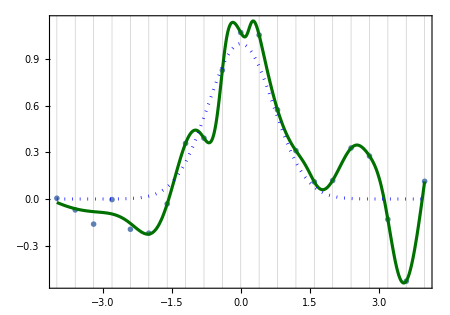
-Graphics-Figure 23. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)

RandomSeeding -> 24 (1/319, 14.1759)

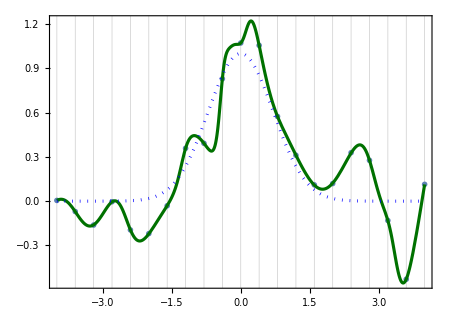
-Graphics-Figure 29. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)

## Section 5: Fitting the DB Data with an InterpolatingFunction[]

```mathematica
noisyGaussianDataDB
```

```mathematica
interpFDBdata = Interpolation[noisyGaussianDataDB, InterpolationOrder->3, Method->"Hermite"]
```

$Line = $Line-1;codeInTextCell[ "Figure",figNo,"shows the InterpolatingFunction-based fitted model with the data in noisyGaussianDataDB" ]

$Line = $Line-1;
Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {interpFDBdata[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];
Labeled[ %, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)
and InterpolationFunction (order->3).
Maximum error zero, integrated curvature `2`.",figNo++, NumberForm[ 7.97094, {6,5} ]], captionStyle] ]//Print;

differences = Table[ interpFDBdata[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

inputGivesOutput[ integratedCurvature[ interpFDBdata, {-4,+4} ] ]

### curvatureFunction[]

As can be seen from their respective definitions, the functions integratedCurvature[] and  curvatureFunction[] are closely related. In the following we calculate and plot the curvature of three differently specified functions.

#### Construct an InterpolatingFunction[]

Here we obtain an InterpolatingFunction[] representation of a function fitted directly to DB’s data. This function provides a “reference” value of the integrated curvature of a smooth function which does pass through all the data points, as shown below.

```mathematica
interpFDBdata = Interpolation[noisyGaussianDataDB, InterpolationOrder->4,Method->"Hermite" ]
```

$Line = $Line-1;codeInTextCell[ "Figure",figNo,"shows the polynomial fitted model of order 12 with the data in noisyGaussianDataDB" ]

$Line = $Line-1;
Show[
 {
ListPlot[ noisyGaussianDataDB, PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[ {interpFDBdata[x], Exp[-x^2]}, {x, -4,4}, PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{Thickness[0.005],Dotted,Blue}},Axes->True ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];
Labeled[ %, Style[ StringForm["Figure `1`. The digitised data with ⅇ^(-SuperscriptBox[x, 2]), (dotted blue)
and InterpolationFunction (Order->3)",figNo++], captionStyle] ]//Print;

differences = Table[ interpFDBdata[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

inputGivesOutput[ integratedCurvature[ interpFDBdata, {-4,+4} ] ]

Note that the differences expressed as Egyptian fractions show that the fitted function interpFDBdata[] does pass through all the given data points.
The integrated curvature is considerably smaller than for any of the ANN fitted functions derived above.

#### Example with Head InterpolatingFunction

This constructs a Symbol kurv such that kurv[x] is the curvature function for the fitted function interpFDBdata[].

```mathematica
kurv =curvatureFunction[ interpFDBdata]/.{s$->x}
```

Scaling the fitted function interpFDBdata[] makes the comparison of the two functions easier.

$Line = $Line-1;
Show[
 {
ListPlot[ Map[ (s↦{s⟦1⟧, 5 s⟦2⟧}),noisyGaussianDataDB], PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[{5 interpFDBdata[x], kurv[x]}, {x, -4,4},
PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{RGBColor[0.880722, 0.611041, 0.142051]}},
PlotRange->All,ImageSize->450,AspectRatio->0.70,PlotLegends->Placed["Expressions",Right],Frame->True, PlotPoints->200,PlotLegends->"Expressions" ]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];
Labeled[ %, Style[ StringForm["Figure `1`. The digitised data with its fitted function (InterpolationFunction of order 3)
and the corresponding curvature function.",figNo++], captionStyle] ]//Print;

This illustrates the discontinuities at two of the data points.

$Line = $Line-1;
inputGivesOutput[ {kurv[0-0.001],kurv[0],kurv[0+0.001]} ]

$Line = $Line-1;
inputGivesOutput[ {kurv[0.8-0.001],kurv[0.8],kurv[0.80+.001]} ]

codeInTextCell999[ {{"Figure",figNo},{"shows that the peak curvature (~7) does not occur exactly at the data point with x = 3.6, as it might appear from Figure",figNo-1},{"above:" }}]

$Line = $Line-1;
Show[
 {
ListPlot[ Map[ (s↦{s⟦1⟧, 5 s⟦2⟧}),noisyGaussianDataDB], PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[{5 interpFDBdata[x], kurv[x]}, {x, -4,4},
PlotStyle→{{Thickness[0.005],Darker[Darker[Green]]},{RGBColor[0.880722, 0.611041, 0.142051]}},
PlotRange->All,ImageSize->450,AspectRatio->0.70,PlotLegends->Placed["Expressions",Right],Frame->True, PlotPoints->200,PlotLegends->"Expressions" ]
},
PlotRange→{{3.4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];
Labeled[ %, Style[ StringForm["Figure `1`. The digitised data with its fitted function (InterpolationFunction of order 3)
and the corresponding curvature function, near x = 3.6.",figNo++], captionStyle] ]//Print;

inputGivesOutput[ {kurv[3.6-0.001],kurv[3.6],kurv[3.6+.001]} ]

There are apparent discontinuities in the curvature function at almost all the date points. The Hermite polynomial fitted function is continuous in its first derivative at each node, but not necessarily in its second derivative.

#### Examples with Head Symbol

For a simple function of the form y=f[x] where f is the Head of a defined Mathematica function and no parameters are needed, the function name only is the required argument of curvatureFunction[].

```mathematica
κ =curvatureFunction[ Sin]/.{s$->x}
```

$Line = $Line-1;
codeInTextCell[ "Figure",figNo,"displays Sin[x] and its corresponding κ[x] together (both unscaled)." ]

```mathematica
2 2
```

$Line = $Line-3;
Plot[ {Sin[x],κ[x]}, {x, -2π,+2π},PlotRange->All, ImageSize->450, PlotLegends->"Expressions", Frame->True ];
Labeled[ %, Style[ StringForm["Figure `1`. Sin[x] with its corresponding curvature function.",figNo++], captionStyle] ]//Print;

```mathematica
2 2
```

Note that …

inputGivesOutput[  κ[0]]

inputGivesOutput[  κ[π/2]]

inputGivesOutput[  κ[ -π/2]]

```mathematica
κ =curvatureFunction[ Gamma]/.{s$->x}
```

$Line = $Line-1;
codeInTextCell[ "Figure",figNo,"displays Gamma[x] and its corresponding κ[x] together (Gamma[x] scaled for ease of comparison)." ]

$Line = $Line-1;
Plot[ {5 Gamma[x],κ[x]}, {x, -3,+3},(*PlotRange->All,*) ImageSize->450, PlotLegends->"Expressions", Frame->True ];
Labeled[ %, Style[ StringForm["Figure `1`. Gamma[x] with its corresponding curvature function.",figNo++], captionStyle] ]//Print;

$Line = $Line-3;
twoAxisPlot[{Gamma[x],κ[x]},{x,-3,3}, PlotLegends->Placed[ {"Gamma[x]","κ[x]"},Right],
(*PlotRange->Full,*)
ImageSize->475];
Labeled[ %, Style[ StringForm["Figure `1`. Gamma[x] with its corresponding curvature function.",figNo++], captionStyle] ]//Print

If a more elaborate specification of the target function is required—e.g., Sin[3x] instead of Sin[x]—the following is an example of how to proceed.
(Sin[3x] has been scaled for easy comparison with its curvature function κ[x].)

```mathematica
Remove[ func ]
func[x_]:=Sin[3 x]
κ =curvatureFunction[ func]/.{s$->x}
```

$Line = $Line-1;codeInTextCell[ "In Figure",figNo,"Sin[3x] (scaled) and its κ[x] are shown together. Curvature values for Sin[3x] are 9 times (two differentiations!) larger than for Sin[x]." ]

$Line = $Line-1;Plot[ {10 func[x]//Evaluate,κ[x]}, {x, -2π,+2π},PlotRange->All, ImageSize->450, PlotLegends->"Expressions", Frame->True ];
Labeled[ %, Style[ StringForm["Figure `1`. Sin[3x] with its corresponding curvature function.",figNo++], captionStyle] ]//Print;

$Line = $Line-3;
twoAxisPlot[{func[x],κ[x]},{x,-3,3}(*, PlotLegends->Placed[ {"func[x]","κ[x]"},Right]*),
(*PlotRange->Full,*)
ImageSize->475];
Labeled[ %, Style[ StringForm["Figure `1`. Gamma[x] with its corresponding curvature function.",figNo++], captionStyle] ]//Print

Note that …

$Line = $Line-2;
inputGivesOutput[  κ[0]]

$Line = $Line-2;
inputGivesOutput[  κ[π/2]]

$Line = $Line-2;
inputGivesOutput[  κ[ -π/2]]

A slightly more elaborate target function.

```mathematica
Remove[ func ]
func[x_]:=ⅇ^(-x/5)Sin[x]
κ =curvatureFunction[ func]/.{s$->x}
```

```mathematica
2 2
```

$Line = $Line-1;codeInTextCell[ "Figure",figNo,"contrasts an exponentaially damped sine function and its κ[x]." ]

```mathematica
2 2
```

$Line = $Line-2;Plot[ {func[x]//Evaluate,κ[x]}, {x, -2π,+2π},PlotRange->All, ImageSize->450, PlotLegends->"Expressions", Frame->True ];
Labeled[ %, Style[ StringForm["Figure `1`. ⅇ^(-x/5)Sin[x] with its corresponding curvature function.",figNo++], captionStyle] ]//Print;

$Line = $Line-3;
twoAxisPlot[{func[x],κ[x]},{x,-2π,2π}(*, PlotLegends->Placed[ {"func[x]","κ[x]"},Right]*),
(*PlotRange->Full,*)
ImageSize->475];
Labeled[ %, Style[ StringForm["Figure `1`. ⅇ^(-x/5)Sin[x] with its corresponding curvature function.",figNo++], captionStyle] ]//Print

Note that …

$Line = $Line-2;
inputGivesOutput[  κ[0]]

$Line = $Line-2;
inputGivesOutput[  κ[π/2]]

$Line = $Line-2;
inputGivesOutput[  κ[-π/2]]

#### Example with Head NetChain

Again we scale curvetrained[x] for ease of comparison with its curvature function.

```mathematica
κ =curvatureFunction[ curvetrained]/.{s$->x}
```

$Line = $Line-1;Plot[ {50 curvetrained[x],κ[x]}, {x, -4,+4},PlotRange->All, ImageSize->450,AspectRatio->0.70, PlotLegends->Placed["Expressions", Right ], Frame->True ];
Labeled[ %, Style[ StringForm["Figure `1`. curvetrained[x] with its corresponding curvature function.",figNo++], captionStyle] ]//Print;

$Line = $Line-1;codeInTextCell999[ {{"Figure",figNo},{"shows the", Style[ twoAxisPlot[] //HoldForm,FontSize→14]},{"version of",figNo-1},{"with the full sclaes for both functions shown (with an x-axis for the blue function)."}} ]

$Line = $Line-1;codeInTextCell999[ {{"Figure",figNo},{"shows a",Style[ twoAxisPlot[] //HoldForm,FontSize→14]}, {"version of Figure",figNo-1},{"with the full scales for both functions shown (with an x-axis for",Style[ curvetrained[] //HoldForm,FontSize→14]}, {"." }}]

$Line = $Line-3;
twoAxisPlot[ {curvetrained[x]//HoldForm,κ[x]//HoldForm},{x,-4,4},
ImageSize->475];
Labeled[ %, Style[ StringForm["Figure `1`. curvetrained[x] with its corresponding curvature function.",figNo++], captionStyle] ]//Print

Note that …

$Line = $Line-2;
inputGivesOutput[  κ[0]]

$Line = $Line-2;
inputGivesOutput[  κ[-0.2]]

$Line = $Line-2;
inputGivesOutput[  κ[ +0.2]]

$Line = $Line-2;
inputGivesOutput[  κ[ -4]]

$Line = $Line-2;
inputGivesOutput[  κ[ +4]]

## Section 6: Fitting & Evaluating Polynomial Models

Experimentation showed that the best compromise in determining the order of a polynomial fitted function that:
(i) gave large maximum errors (order too low), and
(ii) exhibited large and unnecessary excursions between data points (order too high)
was of 12^th order.

```mathematica
polyOrder=13;
nlm=NonlinearModelFit[noisyGaussianDataDB,Array[ coeff, polyOrder].Table[ x^n, {n, 0,polyOrder-1} ],Array[ coeff, 21],x];
Normal[nlm]
```

```mathematica
Remove[ polyModel ]
polyModel[x_] := Normal[nlm]//Evaluate
```

$Line = $Line-1;codeInTextCell[ "Figure",figNo,"shows the polynomial fitted model of order 12 with the data in noisyGaussianDataDB" ]

$Line = $Line-1;
Show[
 {
ListPlot[ Map[ (s↦{s⟦1⟧, s⟦2⟧}),noisyGaussianDataDB], PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[polyModel[x],{x,-4,4},PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70,
PlotLegends->Placed["Expressions",Right]]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];
Labeled[ %, Style[ StringForm["Figure `1`. The digitised data with a best-fit 12^th order polynomial.",figNo++], captionStyle] ]//Print

```mathematica
kurvPoly = curvatureFunction[ polyModel ]/.{s$->x}
```

$Line = $Line-1;codeInTextCell999[ {{"Figure",figNo},{"shows the (scaled) polynomial fitted model of order 12 and its (unscaled) curvature function with the data in", Text[Style["noisyGaussianDataDB",FontSize→14]]},{"."}} ]

$Line = $Line-3;
Show[
 {
ListPlot[ Map[ (s↦{s⟦1⟧, 10 s⟦2⟧}),noisyGaussianDataDB], PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}],
Plot[{10 polyModel[x],kurvPoly[x]},{x,-4,4},PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70,
PlotLegends->Placed["Expressions",Right]]
},
PlotRange→{{-4,4}, All},Axes->True, ImageSize->450, Frame→True, AspectRatio->0.70 ];
Labeled[ %, Style[ StringForm["Figure `1`. The digitised data with a (scaled) best-fit 12^th order polynomial
and its corresponding curvature function.",figNo++], captionStyle] ]//Print

$Line = $Line-1;codeInTextCell[ "Figure",figNo,"—as shown below in the next Program cell—is produced by the IP package function twoAxisPlot[], which allows the two functions to be plotted together with separate scales." ]

Show[
 {
twoAxisPlot[{polyModel[x],kurvPoly[x]},{x,-4,4}, PlotLegends->Placed[ {"polyModel[x]","kurvPoly[x]"},Right],
PlotRange->All,
ImageSize->475,
AspectRatio->0.7],
ListPlot[ Map[ (s↦{s⟦1⟧, s⟦2⟧}),noisyGaussianDataDB], PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}]
},
GridLines→{Table[  k, {k, -4,+4, 0.4}],None}]

$Line = $Line-3;
Show[
 {
twoAxisPlot[{polyModel[x]//HoldForm,kurvPoly[x]//HoldForm},{x,-4,4},
PlotRange->All,
ImageSize->475,
AspectRatio->0.7],
ListPlot[ Map[ (s↦{s⟦1⟧, s⟦2⟧}),noisyGaussianDataDB], PlotMarkers→ ,GridLines→{Table[  k, {k, -4,+4, 0.4}],None}]
},
GridLines→{Table[  k, {k, -4,+4, 0.4}],None}];
Labeled[ %, Style[ StringForm["Figure `1`. The digitised data with a (scaled) best-fit 12^th order polynomial
and its corresponding curvature function.",figNo++], captionStyle] ]//Print

differences = Table[ polyModel[x], {x, -4,+4, 0.4} ]-Map[  Last, noisyGaussianDataDB];
inputGivesOutput[ differences ]

$Line = $Line-1;
inputGivesOutput[ Map[ egyptianFractionSimple, differences] ]

$Line = $Line-1;
inputGivesOutput[ MinMax[Abs[ Map[ egyptianFractionSimple, differences]]] ]

$Line = $Line-1;
inputGivesOutput[ integratedCurvature[ polyModel, {-4,+4} ] ]